# PPPC Machine: combined spectra pipeline

by Flip Tanedo 
with assistance from Jordan Smolinsky & special thanks to David Curtin
based on PPPC4DMID by Marco Cirelli et al, www.marcocirelli.net/PPPC4DMID.html 

If used: please cite Rajaraman, Smolinsky, Tanedo (2015). 

Machine for fitting FERMI diffuse γ-ray spectra to simple models of DM annihilation to (i) 2 quarks, (ii) 2 (axial-)vector mediators that decay to quarks, (iii) 3 pseudoscalar mediators that decay to quarks. We assume that the vectors have universal coupling and the pseudoscalar has mass-weighted coupling so that it is well approximated by a b-philic coupling.

Based on 2to2scanrevised.nb, HeavyHooperonPPPC.nb, 2to3Amplitude.nb

Goal: 
1. output PPPC binned spectra
2. take binned data and compare to PPPC spectra
`	a) compare to a histogram
	b) compare to a histogram with error bars
	c) compare to a histogram with degeneracies
3. Provide tools for batch analysis of a range of spectra from a parameter space scan
	
Required: PPPC files. http://www.marcocirelli.net/PPPC4DMID.html. Download these somewhere and define the path below. See www.marcocirelli.net/PPPC4DMID.html for more details.

Usage: Run this notebook. See PPPCMachineRunner notebook for doing parameter space scan. See PPPCMachineReader notebook for analysis of these outputs.

Remarks:
Feb 13: interpolated functions for on-shell mediators with threshold masses don’t work, e.g. degenerate DM and vector mediator (2-to-2).

### Change Log

Flip’s modifications:
13 Feb 2015: Fixed GetMinA error in the case when A=1 fits. Changed RangeofNorms to sample on a log scale so that it gives even slices over a log-log plot. Actually, had to fix GetMinA again: it can get caught into a never-ending loop if there are no envelope sizes that fit. I put in a hard cutoff at A=10 to stop the loop, so any envelope scaling of 10 should be treated as effectively no envelope. Fixed more greater than/less than errors in this function. Also note that there are some AllTrue functions that don’t exist in Mathematica 9.

11 Feb 2015: Fixed units on Fermi profiles so everything is in GeV. Included “short” code for testing the GetGoodNorms function. Introduced GetMinA functions to find the minimum ‘wiggle room’ needed for a given shape to fit an envelope. Introduced the FullTag function to extract all relevant data from the interpolated spectra.

5 Feb 2015: consolidated some analysis code from PPPC Machine Reader. No need for that to be in a separate place. Including J factor tables from PPPC. “Graveyard” of old code removed, see 25 Jan backup version of code for

26 Jan 2015: re-wrote on normalization code based on Jordan’s techniques. Just broke up the code into smaller functions so that they can be called and debugged independently. Also made them more general (at the cost of more arguments). Defined “bottomless” MinEnv to avoid confusion; the envelope is effectively zero above 14 GeV. Also: don’t ask about envelopes below / above the “data” -- i.e. stay within 1 and 100 GeV, or else “InEnvelope” can give spurious rejections.

24 Jan 2015: qq’ final states. This requires mediators with mass m > mq + mq’, so the case of interest (tc) requires at least ~ 180 GeV

22 Jan 2015: Some changes:
- Added dσvdEfastest which does a discrete sum over mediator energies. Only 2x faster for <1% error. Doesn’t help much?
- Fixed p3ϕ2gamfaster and p3ϕ2gamSwift calls to p2ϕ2gamquick, which no longer needs the primary mass as an argument.
- Tested p3ϕ2gamSwift, gives a factor of ~20 improvement in speed over p3ϕ2gamfaster. Can add another factor of 1.2 if you use dσdvEfastest, but this doesn’t seem worth the trouble.
- Moved Jordan’s functions around so each section is organized coherently.
- TO DO: clean up normalization test code
- TO DO: eventually do the qq’ final states, at least for vectors, maybe just for 2-to-2. 

21 Jan 2015: Minor changes for clarity. Some rearrangements. I was dumb, you don’t need to define interpolating functions that combine different final states---we can always add these together afterward. Jordan’s spectrum checker code isn’t affected by this. 
- Added p2ϕ2gamquickest function as a helper; introduced p2ϕ2gamSwift and p3ϕ2gamSwift, factor of 30 faster. 
- TO DO: test the p3ϕ2gamSwift function---check accuracy. 
- Updated output functions
- TO DO: output functions for 2-to-3 and flavor violation.

Jordan’s modifications:
20 Jan 2015: Cut out the fat and wrote a function to do interpolations for combined spectra
8 Jan 2015: Got the highlighting stuff to work
24 Nov - 5 Dec 2014: Added functions to plot interpolated spectra iff the spectrum fits inside the specified envelope, and also outputs normalization constant

Flip’s original:
24 Nov 2014: Added functions to fit spectra both with exponential of a cubic polynomial and with a power law with exponential cutoff
21 Nov 2014: Attempted to add functions that fit to the spectrum rather than outputting interpolation functions
7-19 Nov 2014: Added function to handle flavor violating modes. Modified SaveIt to only produce the appropriate data files when all the masses make sense
6 Nov 2014: Added some new helper functions for doing runs. Fixed error in p3ϕ2gam functions. Fixed error in p3ϕ2gamfaster: WeightedSpectrum[Egam_] was missing a factor of ΔEϕ. 
4 Nov 2014: this is a streamlined version of PPPC Machine; the idea is that you can just run the notebook to load all relevant functions. Based on the 3 November version. I’ve removed binning functions for now. Added DC’s SaveIt and ReadIt functions.
3 November 2014: Minor bug fixes.
2 Nov 2014: 2-3 spectra, faster 2-2 interpolations 
30 October 2014: kinematics and functions for on-shell mediators
21 October 2014

```mathematica
ClearAll["Global`*"] (* This is just good form *)
```

Code for generating interpolated spectra

## User-specific input

### Input your PPPC location and run

Go to Insert > File Path to insert the path to dldNdlxEW.m 
Note 2/10/2015: don’t bother with JAnn.m, it’s simpler and more accurate to calculate the J factor directly.

```mathematica
(*Get["C:\\Users\\Jordan\\Documents\\My Dropbox\\Irvine\\Research\\Dark Matter GC Gamma Excess\\PPPC4DMID\\dlNdlxEW.m"];*)

Get["/Users/fliptanedo/Documents/Code/PPPC/dlNdlxEW.m"];
(*Get["/Users/fliptanedo/Documents/Code/PPPC/JAnn.m"];*)
```

## Define functions

### Photon spectrum

#### Instructions from PPPC sample file

Fluxes are given as Log_10[(d N)/(d Log_10 x)]  (x = K/m_DM, with K the kinetic energy in GeV)  normalized per single DM annihilation. 
The format is

	dlNdlxIEW[primary -> secondary][mass, lx]

where

	primary = eL, eR, e, μL, μR, μ, τL, τR, τ, q, c, b, t, WL, WT, W, ZL, ZT, Z, g, γ, h, νe, νμ, ντ, V→e, V→μ, V→τ
	secondary = e, p, γ, d, νe, νμ, ντ	
	mass = m_DM in GeV, on the range m_DM= 5 GeV → 100 TeV
	lx = Log[10, x ], on the range x = 10^-9→ 1 except for the channels V→e, V→μ, V→τ for which x = 10^-5→ 1

Warning:	Extrapolations are performed close to the kinematical threshold for massive primaries (e.g. in the case DM DM -> ZZ with m_DM=93 GeV): the output fluxes should be reliable, but instabilities are possible. Also, instabilities very close to the edges of the domain in x are possible.

#### Generic primary to photon spectrum function

pE is the primary energy, i.e. the mass of the DM for pairwise annihilation to SM pairs.

```mathematica
p2gam[primary_,pE_,photonE_]:=If[photonE<pE,
10^(dlNdlxIEW[primary->"γ"][pE,Log[10,photonE/pE]])/(Log[10.] photonE),
0 (* if photon energy is larger than injection energy *)
] (* usage: primary is of the form "τ", WITH the quotation marks *)
```

## Discussion: Boosted Spectra

We give a brief discussion of boosted spectra.

The photon spectrum is given by

dN_γ^tot/dE_γ=∫dE_SM dN_SM^tot/dE_SM (dN_γ(E_SM))/dE_γ

Where the spectrum of Standard Model primaries is a delta function for the case of annihilation of two DM particles into two SM particles. This is fixed purely from kinematics.

In the case of annihilation to on-shell mediators, however, we know that dN_SM^tot/dE_SM has its own spectrum that is a box in the case of two on-shell mediators.

dN_SM^tot/dE_SM=∫dE_ϕ dN_ϕ/dE_ϕ ((dN_SM(E_ϕ))/dE_SM)_lab

Note that ((dN_SM(E_ϕ))/dE_SM)_lab is a box spectrum for a fixed E_ϕ. This is because E_ϕ in the lab frame is

E_ϕ=γ m_ϕ/2+γβ √(m_ϕ^2/4-m_SM^2)Cos[θ]

Where Cos[θ] is the angle with respect to the boost direction. We have to average over this angle to account for the isotropy of the DM annihilation. The boost parameter γ is the boost from the ϕ rest frame to the lab frame. In particular,

γ = E_ϕ/m_ϕ
γβ=√((E_ϕ/m_ϕ)^2-1)

Then, in terms of the unit box function (box of unit length and height, centered around zero,

((dN_SM(E_ϕ))/dE_SM)_lab= (Norm) UnitBox[(E_SM-E_ϕ/2)/(2 √((E_ϕ/m_ϕ)^2-1)√(m_ϕ^2/4-m_SM^2))]
(Norm) =(Number of SM particles per ϕ)/(Width of the box)=2/(2 √((E_ϕ/m_ϕ)^2-1)√(m_ϕ^2/4-m_SM^2))

So ultimately we have

dN_γ^tot/dE_γ=∫dE_SM (∫dE_ϕ dN_ϕ/dE_ϕ (Norm) UnitBox[(E_SM-E_ϕ/2)/(2 √((E_ϕ/m_ϕ)^2-1)√(m_ϕ^2/4-m_SM^2))]) (dN_γ(E_SM))/dE_γ

## Boosted Spectra: 2 to 2

Now we define a set of tools for annihilation modes to two on-shell [vector] mediators which subsequently decay into pairs of SM fermions. 

Notes: I’m not building in any automatic “zero if the kinematics don’t allow on-shell mediators.” Users should be careful.

### Functions

Following my HeavyHooperonPPPC code, I’ll define a full funciton (p2pϕ2gam) which does a numerical integral over the SM final state energies (whose range comes from the boosted mediator). For scans it’s more useful to define an interpolating function for the spectrum

#### Regular: χχ→VV (V→qq) [no longer used]

This is the obvious thing to write, but there are some tricks to make it faster.]

```mathematica
p2ϕ2gam[primary_,mχ_,mϕ_,photonE_]:=Module[
{finalstate=primary,mchi=mχ, mphi=mϕ,eγ=photonE,mSM,γ,γβ, E0, norm,EfsHi,EfsLo},
mSM = Which[finalstate=="t", 173., finalstate=="b", 4.2, finalstate=="c", 1.2, finalstate=="q", 0.01]; 
γ=mchi/mphi;
γβ=√((mchi/mphi)^2-1);
E0=mphi/2;
norm=1/(γβ √((mphi/2)^2-mSM^2));
(*Just a sanity check, the Subscript[dN, ϕ]/Subscript[dE, ϕ] distribution is*)
(*norm UnitBox[(eγ(*temp*) - E0)/(2 γβ √((mphi/2)^2-mSM^2))];*)
EfsHi=γ E0+γβ √((mphi/2)^2-mSM^2);
EfsLo=γ E0-γβ √((mphi/2)^2-mSM^2);
norm NIntegrate[p2gam[finalstate,Efs,eγ],{Efs,EfsLo,EfsHi}]
]
```

#### QUICK: χχ→VV (V→qq) [no longer used]

This uses “SymbolicProcessing->0” in the NIntegrate function and is factor of 8 faster.

```mathematica
(* alternate version with "SymbolicProcessing->0", factor of 8 faster *)
p2ϕ2gamquick[primary_,mχ_,mϕ_,photonE_]:=Module[
{finalstate=primary,mchi=mχ, mphi=mϕ,eγ=photonE,mSM,γ,γβ, E0, norm,EfsHi,EfsLo},
mSM = Which[finalstate=="t", 173., finalstate=="b", 4.2, finalstate=="c", 1.2, finalstate=="q", 0.01];
γ=mchi/mphi;
γβ=√((mchi/mphi)^2-1);
E0=mphi/2;
norm=1/(γβ √((mphi/2)^2-mSM^2));
(*Just a sanity check, the Subscript[dN, ϕ]/Subscript[dE, ϕ] distribution is*)
(*norm UnitBox[(eγ(*temp*) - E0)/(2 γβ √((mphi/2)^2-mSM^2))];*)
EfsHi=γ E0+γβ √((mphi/2)^2-mSM^2);
EfsLo=γ E0-γβ √((mphi/2)^2-mSM^2);
norm NIntegrate[p2gam[finalstate,Efs,eγ],{Efs,EfsLo,EfsHi},Method->{Automatic,"SymbolicProcessing"->0}]//Quiet (* seems to give slow convergence warnings, only off at 4th decimal? *)
]
```

#### QUICKEST: χχ→VV (V→qq) [Discretizes integral]

Some quick tests with b-quark final staes: with nEfs=10 samplings, you the result is within one precent accuracy and almost 30 times faster. Tested with b quark final states (80 GeV DM going to 20 GeV mediators). You can go with nEfs=20 samplings to be safe, but this is probably overkill. 

Since there is a flat distribution in the primary energy, you can get away with fairly low number of samplings.

I should also add this to the flavor-violating final state, but that one doesn’t have much parameter space to worry about anyway, so I’ll leave it as is.

Note: p2ϕ2gamquickest also includes the map between primary and its mass.

```mathematica
p2ϕ2gamquickest[primary_,mχ_,mϕ_,nEfs_,photonE_]:=Module[
{finalstate=primary,mchi=mχ, mphi=mϕ,eγ=photonE,mSM,γ,γβ, E0, norm,EfsHi,EfsLo,numEfs=nEfs,rangeEfs},

mSM = Which[finalstate=="t", 173., finalstate=="b", 4.2, finalstate=="c", 1.2, finalstate=="q", 0.01];

γ=mchi/mphi;
γβ=√((mchi/mphi)^2-1);
E0=mphi/2;
norm=1/(γβ √((mphi/2)^2-mSM^2));
(*Just a sanity check, the Subscript[dN, ϕ]/Subscript[dE, ϕ] distribution is*)
(*norm UnitBox[(eγ(*temp*) - E0)/(2 γβ √((mphi/2)^2-mSM^2))];*)
EfsHi=γ E0+γβ √((mphi/2)^2-mSM^2);
EfsLo=γ E0-γβ √((mphi/2)^2-mSM^2);
(*norm NIntegrate[p2gam[finalstate,Efs,eγ],{Efs,EfsLo,EfsHi},Method->{Automatic,"SymbolicProcessing"->0}]//Quiet *)
(* seems to give slow convergence warnings, only off at 4th decimal? *)

rangeEfs=Range[EfsLo+(EfsHi-EfsLo)/(2numEfs),EfsHi,(EfsHi-EfsLo)/numEfs];
norm  (EfsHi-EfsLo)/numEfs Total[p2gam[finalstate,#,eγ]&/@rangeEfs]
]
```

#### Old: χχ→VV V→qq’ [not used]

This gives the γ spectrum for boosted mediators which can decay into flavor violating quark pairs. In particular, you might be interested in the decay into top-charm.

```mathematica
diffquarkstogammafull[flavor1_, flavor2_, mchi_, mphi_, photonenergy_]:=
Module[{mχ = mchi, mϕ = mphi, eγ = photonenergy, γ, β, Eq10, Eq20, mq1, mq2, Eq1low, Eq1high, Eq2low, Eq2high, norm1, norm2}, mq1 = Which[flavor1=="t", 173., flavor1=="b", 4.2, flavor1=="c", 1.2, flavor1=="q", 0.01]; (* heavy quark masses *)
mq2 = Which[flavor2=="t", 173., flavor2=="b", 4.2, flavor2=="c", 1.2, flavor2=="q", 0.01];
γ = mχ/mϕ;
β=√(1-(mϕ/mχ)^2);
(* the energies of the emitted particles in the ϕ rest frame *)
Eq10 = mϕ/2+(mq1^2-mq2^2)/(2 mϕ);
Eq20 = mϕ/2+(mq2^2-mq1^2)/(2 mϕ);
(* the min and max energies of the emitted particles in the lab frame *)
Eq1low=γ (Eq10-β √(Eq10^2-mq1^2));
Eq2low = γ(Eq20-β √(Eq20^2 - mq2^2));
Eq1high=γ (Eq10+β √(Eq10^2-mq1^2));
Eq2high=γ (Eq20+β √(Eq20^2-mq2^2));
norm1= 1/(2β γ √(Eq10^2-mq1^2));
norm2 = 1/(2β γ √(Eq20^2-mq2^2));

(* output *)
0.5 norm1 NIntegrate[p2gam[flavor1, Eq1, eγ], {Eq1, Eq1low, Eq1high}]+0.5norm2 NIntegrate[p2gam[flavor2, Eq2, eγ], {Eq2, Eq2low, Eq2high}]]


diffquarkstogammaquick[flavor1_, flavor2_, mchi_, mphi_, photonenergy_]:=
Module[{mχ = mchi, mϕ = mphi, eγ = photonenergy, γ, β, Eq10, Eq20, mq1, mq2, Eq1low, Eq1high, Eq2low, Eq2high, norm1, norm2}, mq1 = Which[flavor1=="t", 173., flavor1=="b", 4.2, flavor1=="c", 1.2, flavor1=="q", 0.01]; (* heavy quark masses *)
mq2 = Which[flavor2=="t", 173., flavor2=="b", 4.2, flavor2=="c", 1.2, flavor2=="q", 0.01];
γ = mχ/mϕ;
β=√(1-(mϕ/mχ)^2);
(* the energies of the emitted particles in the ϕ rest frame *)
Eq10 = mϕ/2+(mq1^2-mq2^2)/(2 mϕ);
Eq20 = mϕ/2+(mq2^2-mq1^2)/(2 mϕ);
(* the min and max energies of the emitted particles in the lab frame *)
Eq1low=γ (Eq10-β √(Eq10^2-mq1^2));
Eq2low = γ(Eq20-β √(Eq20^2 - mq2^2));
Eq1high=γ (Eq10+β √(Eq10^2-mq1^2));
Eq2high=γ (Eq20+β √(Eq20^2-mq2^2));
norm1= 1/(2β γ √(Eq10^2-mq1^2));
norm2 = 1/(2β γ √(Eq20^2-mq2^2));

(* output *)
0.5 norm1( NIntegrate[p2gam[flavor1, Eq1, eγ], {Eq1, Eq1low, Eq1high}, Method->{Automatic, "SymbolicProcessing"->0}]//Quiet)+0.5norm2 (NIntegrate[p2gam[flavor2, Eq2, eγ], {Eq2, Eq2low, Eq2high}, Method->{Automatic, "SymbolicProcessing"->0}]//Quiet)]
```

#### QUICKEST: χχ→VV V→qq’

Define “different quarks” version. nEfs = 20 seems to work well, valid to the 5th decimal.

```mathematica
dqp2ϕ2gamquickest[flavor1_, flavor2_, mchi_, mphi_,nEfs_, photonenergy_]:=
Module[{mχ = mchi, mϕ = mphi, eγ = photonenergy, γ, β, Eq10, Eq20, mq1, mq2, Eq1low, Eq1high, Eq2low, Eq2high, norm1, norm2,numEfs=nEfs,rangeEfs1,rangeEfs2}, mq1 = Which[flavor1=="t", 173., flavor1=="b", 4.2, flavor1=="c", 1.2, flavor1=="q", 0.01]; (* heavy quark masses *)
mq2 = Which[flavor2=="t", 173., flavor2=="b", 4.2, flavor2=="c", 1.2, flavor2=="q", 0.01];
γ = mχ/mϕ;
β=√(1-(mϕ/mχ)^2);
(* the energies of the emitted particles in the ϕ rest frame *)
Eq10 = mϕ/2+(mq1^2-mq2^2)/(2 mϕ);
Eq20 = mϕ/2+(mq2^2-mq1^2)/(2 mϕ);
(* the min and max energies of the emitted particles in the lab frame *)
Eq1low=γ (Eq10-β √(Eq10^2-mq1^2));
Eq2low = γ(Eq20-β √(Eq20^2 - mq2^2));
Eq1high=γ (Eq10+β √(Eq10^2-mq1^2));
Eq2high=γ (Eq20+β √(Eq20^2-mq2^2));
norm1= 1/(β γ √(Eq10^2-mq1^2));
norm2 = 1/(β γ √(Eq20^2-mq2^2));

rangeEfs1=Range[Eq1low+(Eq1high-Eq1low)/(2numEfs),Eq1high,(Eq1high-Eq1low)/numEfs];
rangeEfs2=Range[Eq2low+(Eq2high-Eq2low)/(2numEfs),Eq2high,(Eq2high-Eq2low)/numEfs];


(* output *)
(*0.5 norm1( NIntegrate[p2gam[flavor1, Eq1, eγ], {Eq1, Eq1low, Eq1high}, Method->{Automatic, "SymbolicProcessing"->0}]//Quiet)+0.5norm2 (NIntegrate[p2gam[flavor2, Eq2, eγ], {Eq2, Eq2low, Eq2high}, Method->{Automatic, "SymbolicProcessing"->0}]//Quiet)]*)

(* discretize *)
0.5 norm1 (Eq1high-Eq1low)/numEfs Total[p2gam[flavor1, #, eγ]&/@rangeEfs1]+0.5 norm2 (Eq1high-Eq1low)/numEfs Total[p2gam[flavor2, #, eγ]&/@rangeEfs2]]
```

### Fast Functions

p2ϕ2gam takes a long time to plot and, on top of that, can be tempramental when making log plots. So we’ll follow our approach in HeavyHooperonPPPC.nb and create an interpolating function so that the PPPC functions don’t have to be called over and over again. (I believe this saves a lot of time since it doesn’t have to re-interpolate?) Either way, this has been shown to speed things up nicely. Points are spaced evernly on a log scale. I found that 100 points work well, Anthony found that fewer points are also ok.

minE and maxE is the range of photon energies over which we’d like to interpolate
numpoints is the number of points to sample, I use 100

#### V → qq: not so fast [not used]

```mathematica
p2ϕ2gamfast[primary_,mchi_,mphi_,minE_,maxE_,numpoints_]:=Module[
{prim=primary,mχ=mchi,mϕ=mphi,mine=minE,maxe=maxE, samplepoints},

samplepoints=10^#&/@Range[Log[10,minE],Log[10,maxE],(Log[10,maxE]-Log[10,minE])/numpoints];

(* Output *)
Interpolation[{#,p2ϕ2gam[prim,mχ,mϕ,#]}&/@samplepoints]
] (* usage: f=b2gamfast[...]. f[Subscript[E, γ]] gives the number of photons with E=Subscript[E, γ]. *)



(* faster version that uses p2ϕ2gamquick, defined with "SymbolicProcessing"->0 *)
p2ϕ2gamfastest[primary_,mchi_,mphi_,minE_,maxE_,numpoints_]:=Module[
{prim=primary,mχ=mchi,mϕ=mphi,mine=minE,maxe=maxE, samplepoints},

samplepoints=10^#&/@Range[Log[10,minE],Log[10,maxE],(Log[10,maxE]-Log[10,minE])/numpoints];

(* Output *)
Interpolation[{#,p2ϕ2gamquick[prim,mχ,mϕ,#]}&/@samplepoints]
] (* usage: f=b2gamfast[...]. f[Subscript[E, γ]] gives the number of photons with E=Subscript[E, γ]. *)
```

#### V → qq

Redefine p2ϕ2gamfastest to use p2ϕ2gamquickest[primary_,mχ_,mϕ_,nEfs_,photonE_]. I suggest nEfs = 20, this is the number of samplings for range of primary energies. 

Doing a quick test: for 80 GeV DM/20 GeV mediators, the “Swift” function is a little wobbly above 40 GeV if you only use nEfs=10. If you push to nEfs=20 it smooths out and is fairly close to the “fastest” function.

```mathematica
(* faster version that uses p2ϕ2gamquick, defined with "SymbolicProcessing"->0 *)
p2ϕ2gamSwift[primary_,mchi_,mphi_,minE_,maxE_,numpoints_,nEfs_]:=Module[
{prim=primary,mχ=mchi,mϕ=mphi,mine=minE,maxe=maxE, samplepoints,numEfs=nEfs},

samplepoints=10^#&/@Range[Log[10,minE],Log[10,maxE],(Log[10,maxE]-Log[10,minE])/numpoints];
(* Output *)
(*Interpolation[{#,p2ϕ2gamquick[prim,mχ,mϕ,#]}&/@samplepoints]*)
Interpolation[{#,p2ϕ2gamquickest[prim,mχ,mϕ,numEfs,#]}&/@samplepoints]
] (* usage: f=b2gamfast[...]. f[Subscript[E, γ]] gives the number of photons with E=Subscript[E, γ]. *)
```

#### V → qq’: not so fast [not used]

```mathematica
diffquarkstogammafast[flavor1_, flavor2_, mchi_, mphi_, minE_, maxE_, numpoints_] :=Module[{prim1 = flavor1, prim2=flavor2, mχ=mchi, mϕ=mphi, mine=minE, maxe=maxE, samplepoints}, 
samplepoints=10^#&/@Range[Log[10,minE],Log[10,maxE],(Log[10,maxE]-Log[10,minE])/numpoints];
(* Output *)
Interpolation[{#,diffquarkstogammafull[prim1, prim2,mχ,mϕ,#]}&/@samplepoints]
] (* usage: f=b2gamfast[...]. f[Subscript[E, γ]] gives the number of photons with E=Subscript[E, γ]. *)

diffquarkstogammafastest[flavor1_, flavor2_, mchi_, mphi_, minE_, maxE_, numpoints_] :=Module[{prim1 = flavor1, prim2=flavor2, mχ=mchi, mϕ=mphi, mine=minE, maxe=maxE, samplepoints}, 
samplepoints=10^#&/@Range[Log[10,minE],Log[10,maxE],(Log[10,maxE]-Log[10,minE])/numpoints];
(* Output *)
Interpolation[{#,diffquarkstogammaquick[prim1, prim2,mχ,mϕ,#]}&/@samplepoints]
] (* usage: f=b2gamfast[...]. f[Subscript[E, γ]] gives the number of photons with E=Subscript[E, γ]. *)
```

#### V → qq’

This matches pretty well with the ‘fast’ function but is 1000 times faster. Yes, 1000.

```mathematica
dqp2ϕ2gamSwift[flavor1_, flavor2_, mchi_, mphi_, minE_, maxE_, numpoints_,nEfs_] :=Module[{prim1 = flavor1, prim2=flavor2, mχ=mchi, mϕ=mphi, mine=minE, maxe=maxE, samplepoints,numEfs=nEfs}, 
samplepoints=10^#&/@Range[Log[10,minE],Log[10,maxE],(Log[10,maxE]-Log[10,minE])/numpoints];
(* Output *)
Interpolation[{#,dqp2ϕ2gamquickest[prim1, prim2,mχ,mϕ,numEfs,#]}&/@samplepoints]
] (* usage: f=b2gamfast[...]. f[Subscript[E, γ]] gives the number of photons with E=Subscript[E, γ]. *)
```

## Boosted Spectra: 2-to-3

This section is based on 2to3Amplitude.nb. Here we assume annihilation into three mediators is the dominant annihilation mode. We’ve worked out the amplitude and everything. See the other notebook for testing.

### The Amplitude

The amplitude is scaled by g^3. Note that there’s a factor of 2 to account for C12 = C21, etc.

```mathematica
p[Ei_,Mi_]:=√(Ei^2-Mi^2)
C12[E1_,E2_,cos_,Mϕ_,m_]:=E1 E2 -p[E1,Mϕ]p[E2,Mϕ] cos
C13[E1_,E2_,cos_,Mϕ_,m_]:=2m E1 - Mϕ^2-C12[E1,E2,cos,Mϕ,m]
C23[E1_,E2_,cos_,Mϕ_,m_]:=2m E2- Mϕ^2-C12[E1,E2,cos,Mϕ,m]
D12[E1_,E2_,cos_,Mϕ_,m_]:=(Mϕ^2-2 m E1)(Mϕ^2-2 m E2)
D13[E1_,E2_,cos_,Mϕ_,m_]:=(Mϕ^2-2 m E1)(Mϕ^2-2 m (2 m - E1 - E2))
D23[E1_,E2_,cos_,Mϕ_,m_]:=(Mϕ^2-2 m E2)(Mϕ^2-2 m (2 m - E1 - E2))

M[E1_,E2_,cos_,Mϕ_,m_]:=-(2m) 2(C12[E1,E2,cos,Mϕ,m]/D12[E1,E2,cos,Mϕ,m]+C13[E1,E2,cos,Mϕ,m]/D13[E1,E2,cos,Mϕ,m]+C23[E1,E2,cos,Mϕ,m]/D23[E1,E2,cos,Mϕ,m]) (* times g^3 *)
```

### Kinematics notes, not used

These correspond to acceptable of cosine theta. First, the range of E_2 depends on the value of E_1 and the CM energy 2m as follows:

E_1^max=(2m)/2-(3 Mϕ^2)/(2 (2m))

let ξ(E1,E2,cθ)=E1+E2+√(p1^2+p2^2+p1 p2 cθ + Mϕ^2),
the total energy of the final states

if ξ(E1,0,-1) > (2m), then the limits are the solutions to 
ξ(E1,E2,-1)=2m

otherwise, the limits are solutions to 
ξ(E1,E2,+1)=2m
ξ(E1,E2,-1)=2m

```mathematica
ξ[E1_,E2_,cθ_]:=E1+E2+√((E1^2-Mϕ^2)+(E2^2-Mϕ^2)+2 √(E1^2-Mϕ^2)√(E2^2-Mϕ^2)cθ +Mϕ^2)
```

### Define some useful functions

```mathematica
Etot[E1_,E2_,cθ_,Mϕ_]:=E1+E2+√((E1^2-Mϕ^2)+(E2^2-Mϕ^2)+2 √(E1^2-Mϕ^2)√(E2^2-Mϕ^2)cθ +Mϕ^2)
MaxE1[m_,Mϕ_]:=(2 m)/2-(3 Mϕ^2)/(2 2m)
IsCaseI[E1_,m_,Mϕ_]:=Etot[E1,Mϕ,-1,Mϕ]>2 m
MaxE2[E1_,m_,Mϕ_]:=E2x/.Solve[Etot[E1,E2x,-1,Mϕ]==2m,E2x]//Max
MinE2[E1_,m_,Mϕ_]:=If[IsCaseI[E1,m,Mϕ],
E2x/.Solve[Etot[E1,E2x,-1,Mϕ]==2m,E2x]//Min
,
E2x/.Solve[Etot[E1,E2x,+1,Mϕ]==2m,E2x]//Min]

(* Amplitude depends on Cos[θ] which is fixed by kinematics *)
costheta[E1_,E2_,m_,Mϕ_]:=((2m-E1-E2)^2-(E1^2-Mϕ^2)-(E2^2-Mϕ^2)-Mϕ^2)1/(2 √(E1^2-Mϕ^2) √(E2^2-Mϕ^2))
```

### Do Momentum Integral

Factor of 3 coming from the multiplicity of final states. Note that this is NOT dN/dE, this is d<sigma v> / dE.

Symbolic Processing ->0 trick: http://mathematica.stackexchange.com/questions/8768/methods-to-speed-up-numerical-ndsolve-nintegrate

```mathematica
dσvdE[E1_,m_,Mϕ_]:=3NIntegrate[M[E1,E2,costheta[E1,E2,m,Mϕ],Mϕ,m]^2,{E2,MinE2[E1,m,Mϕ],MaxE2[E1,m,Mϕ]}]

(* slightly faster if I use SymbolicProcessing -> 0  *)
dσvdEfast[E1_,m_,Mϕ_]:=3NIntegrate[M[E1,E2,costheta[E1,E2,m,Mϕ],Mϕ,m]^2,{E2,MinE2[E1,m,Mϕ],MaxE2[E1,m,Mϕ]},Method->{Automatic,"SymbolicProcessing"->0}]
```

#### Introduce discretized sum vs. integral... only a factor of 2 in speed (not used)

I tried numE2 = 10 for discretization. I’m only looking for percent accuracy. At around numE2 = 30 the computation time is the same. For numE2 = 5 the accuracy is still percent level but the gain is only about a factor of 2 in speed. Even a numE2 = 3 is reasonable. 

It’s not clear that this increase by a factor of 2 buys much in terms of overall speed.

```mathematica
dσvdEfastest[En1_,mDM_,Mmed_,nE2_]:=Module[
{E1=En1,m=mDM,Mϕ=Mmed,numE2=nE2},
E2Lo=MinE2[E1,m,Mϕ];
E2Hi=MaxE2[E1,m,Mϕ];
rangeE2=Range[E2Lo+(E2Hi-E2Lo)/(2numE2),E2Hi,(E2Hi-E2Lo)/numE2];

(*3NIntegrate[M[E1,E2,costheta[E1,E2,m,Mϕ],Mϕ,m]^2,{E2,MinE2[E1,m,Mϕ],MaxE2[E1,m,Mϕ]},Method->{Automatic,"SymbolicProcessing"->0}]*)
3(E2Hi-E2Lo)/numE2 Total[M[E1,#,N[costheta[E1,#,m,Mϕ]],Mϕ,m]^2&/@rangeE2]
]
```

### Doing the cross section integral: not used in p3ϕ2gam fast

The above plots are not normalized---we ultimately want dN/dE. We’ll need to integrate them to normalize. Note that it’s hard to directly NIntegrate dNdE because Mathematica gets confused by the symolic limits of the E2 integral. We fix this by defining a new function which only takes numbers. See: http://stackoverflow.com/questions/18903010/mathematica-wont-nintegrate-a-conditional-function

```mathematica
dσvdEnum[E1_?NumericQ,m_?NumericQ,Mϕ_?NumericQ]:=dσvdE[E1,m, Mϕ]
(*NIntegrate[dσvdEnum[x,120,45],{x,45,MaxE1[120,45]}]//Timing*)
```

### The total spectrum: nice, but not used--too slow

This might be a helpful tip: http://mathematica.stackexchange.com/questions/10533/nested-nintegrate

Nov 6 , the normalization is off: have to account for 3 final states. This info which is in dσvdEnum, but which is washed out when I normalized by Totalσv. Then I have to account for the fact that the boxnorm is normalized to 2 final state mediators.

```mathematica
p3ϕ2gam[primary_,mχ_,mϕ_,photonE_]:=Module[
{finalstate=primary,mchi=mχ, mphi=mϕ,eγ=photonE,mSM, γ,γβ, E0, boxnorm, Totalσv,Ephi,EfsHi,EfsLo,InnerIntegrand,OuterIntegrand},
mSM=Which[finalstate=="t", 173., finalstate=="b", 4.2, finalstate=="c", 1.3, finalstate=="q", 0];
γ[Eϕ_]:=Eϕ/mphi;
γβ[Eϕ_]:=√((Eϕ/mphi)^2-1);
E0=mphi/2;
boxnorm[Eϕ_]:=1/(2 (*normalize*)γβ[Eϕ] √((mphi/2)^2-mSM^2));
Totalσv=NIntegrate[dσvdEnum[Ephi,mchi,mphi],{Ephi,mphi,MaxE1[mchi,mphi]}];
EfsHi[Eϕ_]:=γ[Eϕ] E0+γβ[Eϕ] √((mphi/2)^2-mSM^2);
EfsLo[Eϕ_]:=γ[Eϕ] E0-γβ[Eϕ] √((mphi/2)^2-mSM^2);
InnerIntegrand[Efs_?NumericQ]:=p2gam[finalstate,Efs,eγ];
OuterIntegrand[Ephi_?NumericQ]:=boxnorm[Ephi]NIntegrate[InnerIntegrand[Efs],{Efs,EfsLo[Ephi],EfsHi[Ephi]}];
(3 (* norm *))/Totalσv NIntegrate[OuterIntegrand[Ephi],{Ephi,mphi,MaxE1[mchi,mphi]}]

(* the versions below work, but they give a bunch of warnings... they end up being off at the 3rd decimal *)
(*1/Totalσv NIntegrate[boxnorm[Ephi] p2gam[finalstate,Efs,eγ],{Ephi,mphi,MaxE1[mchi,mphi]},{Efs,EfsLo[Ephi],EfsHi[Ephi]}]*)

(*real version:*)
(*1/Totalσv NIntegrate[boxnorm[Ephi]NIntegrate[p2gam[finalstate,Efs,eγ],{Efs,EfsLo[Ephi],EfsHi[Ephi]}],{Ephi,mphi,MaxE1[mchi,mphi]}]*)
]
```

### 2 to 3 Faster

First define a discrete version of p3ϕ2gam where we don’t need to calculate Totalσv or do a full numerical integra over Eϕ. Further, we’ll just appeal to p2ϕ2gamFast. The idea is that p3ϕ2gam can be approximated as the weighted average of many p2ϕ2gam functions where mχ is varied to match Eϕ.

Some testing: nϕbins = 5 is too small, nϕbins=20 agrees to the third decimal for a reasonable test value. From previous tests, Nγ should be at least 50.

“Combined” function allows for multiple final states with branching ratios given by a weights vector.
Note: One way to make this even faster is to define a p2ϕ2gamquickest that samples instead of NIntegrates (yes, p2ϕ2gam). Update: I’ve now implemented this in the “Swift” function. Again, I suggest at least nEfs = 20 based on the behavior of the 2-to-2 case.

#### p3ϕ2gamfaster [no longer used]

Takes around 45 seconds.

```mathematica
p3ϕ2gamfaster[SMprimary_,mχ_,mϕ_,minEγ_,maxEγ_,nϕbins_,nγbins_]:=Module[
{primary=SMprimary,mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Nphi=nϕbins,Ngam=nγbins,mSM,
minEphi,maxEphi,ΔEϕ,Eϕmidpoints,dσvdEsamples,totalσv,WeightedSpectrum,samplepoints},
(* Identify points to sample in Eϕ *)

mSM=Which[primary=="t", 173., primary=="b", 4.2, primary=="c", 1.3, primary=="q", 0];

minEphi=mϕ;
maxEphi=MaxE1[mchi,mphi];
ΔEϕ=(maxEphi-minEphi)/Nphi;
Eϕmidpoints=(#[[1]]+#[[2]])/2&/@Partition[Range[minEphi,maxEphi,ΔEϕ],2,1];

(* Sample dσv/dE, also do box approximation to intergal *)
dσvdEsamples={#,dσvdEfast[#,mchi,mphi]}&/@Eϕmidpoints;

totalσv=ΔEϕ Total[#[[2]]&/@dσvdEsamples]; 
(* note that totalσv includes the factor of 3 for the 3x2 final state SM particles vs. only 2 final state SM particles. I have to multiply by 3 again down the road. *)
WeightedSpectrum[Egam_]:=Total[((3 (* 3x2 final particles *) #[[2]] ΔEϕ)/totalσv p2ϕ2gamquick[primary,#[[1]],mphi,Egam]/(2 (* because p2ϕ2gam is normed to 2 mediators *)))&/@dσvdEsamples];
(*NB: one way to make this even faster is to define a p2ϕ2gamquickest that samples instead of NIntegrates *)


(* Identify log sampling in Eγ *)
samplepoints=10^#&/@Range[Log[10,minEgam],Log[10,maxEgam],(Log[10,maxEgam]-Log[10,minEgam])/Ngam];

(* Output an interpolated function *)
Interpolation[{#,WeightedSpectrum[#]}&/@samplepoints]
]
```

#### p3ϕ2gamSwift using p2ϕ2gamquickest

Comparison to p3ϕ2gamfaster: Looks really good. Takes only 3 seconds where previous function took 45. The gain came from using p2ϕ2gamquickest. A good fit: nϕbins = 30, nγbins = 100, nEfs=20. Can probably relax these a bit, but be sure to test against  p3ϕ2gamfaster with conservative numbers (which takes about a minute to run).

```mathematica
p3ϕ2gamSwift[SMprimary_,mχ_,mϕ_,minEγ_,maxEγ_,nϕbins_,nγbins_,nEfs_]:=Module[
{primary=SMprimary,mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Nphi=nϕbins,Ngam=nγbins,mSM,
minEphi,maxEphi,ΔEϕ,Eϕmidpoints,dσvdEsamples,totalσv,WeightedSpectrum,samplepoints,numEfs=nEfs},
(* Identify points to sample in Eϕ *)
mSM=Which[primary=="t", 173., primary=="b", 4.2, primary=="c", 1.3, primary=="q", 0];
minEphi=mϕ;
maxEphi=MaxE1[mchi,mphi];
ΔEϕ=(maxEphi-minEphi)/Nphi;
Eϕmidpoints=(#[[1]]+#[[2]])/2&/@Partition[Range[minEphi,maxEphi,ΔEϕ],2,1];

(* Sample dσv/dE, also do box approximation to intergal *)
dσvdEsamples={#,dσvdEfast[#,mchi,mphi]}&/@Eϕmidpoints;
(* The following can speed things up by an O(20%) amount, not really worth it *)
(*dσvdEsamples={#,dσvdEfastest[#,mchi,mphi,2]}&/@Eϕmidpoints;*)

totalσv=ΔEϕ Total[#[[2]]&/@dσvdEsamples]; 
(* note that totalσv includes the factor of 3 for the 3x2 final state SM particles vs. only 2 final state SM particles. I have to multiply by 3 again down the road. *)
WeightedSpectrum[Egam_]:=Total[((3 (* 3x2 final particles *) #[[2]] ΔEϕ)/totalσv p2ϕ2gamquickest[primary,#[[1]],mphi,numEfs,Egam]/(2 (* because p2ϕ2gam is normed to 2 mediators *)))&/@dσvdEsamples];
(*NB: one way to make this even faster is to define a p2ϕ2gamquickest that samples instead of NIntegrates *)


(* Identify log sampling in Eγ *)
samplepoints=10^#&/@Range[Log[10,minEgam],Log[10,maxEgam],(Log[10,maxEgam]-Log[10,minEgam])/Ngam];

(* Output an interpolated function *)
Interpolation[{#,WeightedSpectrum[#]}&/@samplepoints]
]
```

#### dqp3ϕ2gamSwift

Checked against p3ϕ2gamSwift when the primaries are set to be the same.

```mathematica
dqp3ϕ2gamSwift[SMprimary1_,SMprimary2_,mχ_,mϕ_,minEγ_,maxEγ_,nϕbins_,nγbins_,nEfs_]:=Module[
{primary1=SMprimary1,primary2=SMprimary2,mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Nphi=nϕbins,Ngam=nγbins,
minEphi,maxEphi,ΔEϕ,Eϕmidpoints,dσvdEsamples,totalσv,WeightedSpectrum,samplepoints,numEfs=nEfs},
(* Identify points to sample in Eϕ *)
minEphi=mϕ;
maxEphi=MaxE1[mchi,mphi];
ΔEϕ=(maxEphi-minEphi)/Nphi;
Eϕmidpoints=(#[[1]]+#[[2]])/2&/@Partition[Range[minEphi,maxEphi,ΔEϕ],2,1];

(* Sample dσv/dE, also do box approximation to intergal *)
dσvdEsamples={#,dσvdEfast[#,mchi,mphi]}&/@Eϕmidpoints;
(* The following can speed things up by an O(20%) amount, not really worth it *)
(*dσvdEsamples={#,dσvdEfastest[#,mchi,mphi,2]}&/@Eϕmidpoints;*)

totalσv=ΔEϕ Total[#[[2]]&/@dσvdEsamples]; 
(* note that totalσv includes the factor of 3 for the 3x2 final state SM particles vs. only 2 final state SM particles. I have to multiply by 3 again down the road. *)
WeightedSpectrum[Egam_]:=Total[((3 (* 3x2 final particles *) #[[2]] ΔEϕ)/totalσv dqp2ϕ2gamquickest[primary1,primary2,#[[1]],mphi,numEfs,Egam]/(2 (* because p2ϕ2gam is normed to 2 mediators *)))&/@dσvdEsamples];
(*NB: one way to make this even faster is to define a p2ϕ2gamquickest that samples instead of NIntegrates *)


(* Identify log sampling in Eγ *)
samplepoints=10^#&/@Range[Log[10,minEgam],Log[10,maxEgam],(Log[10,maxEgam]-Log[10,minEgam])/Ngam];

(* Output an interpolated function *)
Interpolation[{#,WeightedSpectrum[#]}&/@samplepoints]
]
```

## DC’s SaveIt and ReadIt functions

http://www.terpconnect.umd.edu/%7Edcurtin1/mathematica.html
See also DumpSave, http://mathematica.stackexchange.com/questions/1959/how-do-i-save-a-variable-or-function-definition-to-a-file
... but DC says this carries the risk of overwriting things because Mathematica saves the initial variable assignment, not just the object itself.

Functions courtesy of David Curtin.

```mathematica
(* to avoid memory bloat *)
ClearMemory:=Module[{},Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];];

SaveIt[filename_,expr_]:=Module[{output},
output=Export[filename<>".dat",ToString[expr//InputForm],"String"];
ClearMemory;
output];
SaveIt[varnamestring_]:=Module[{output},output=Export[varnamestring<>".dat",ToString[ToExpression[varnamestring]//InputForm],"String"];
ClearMemory;
output];

ReadIt[filename_]:=Module[{output},output=ToExpression[Import[StringReplace[filename,".dat"->""]<>".dat","String"]];
ClearMemory;
output];
```

### Reading files: Jordan’s simplified functions

```mathematica
Filetofunction[filename_]:=ReadIt[StringDrop[filename, -4]][[2]]

Filetotag[filename_]:=ReadIt[StringDrop[filename, -4]][[1]]

Listoffilestolistoffunctions[listoffilenames_]:=Filetofunction[#]&/@(DeleteCases[listoffilenames, Null])
```

## Output one data file per function

Makes it easier if I have to halt at some mid point.

### Older versions (not used)

```mathematica
Interpol3phi[SMprimary_,mprimary_,mχ_,mϕ_,minEγ_,maxEγ_,nϕbins_,nγbins_,filename_]:=Module[
{primary=SMprimary,mSM=mprimary,mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Nphi=nϕbins,Ngam=nγbins,path=filename},
SaveIt[path<>"_"<>ToString[mchi]<>"_"<>ToString[mphi],{{primary,mSM,mchi,mphi,minEgam,maxEgam,Nphi,Ngam,path},p3ϕ2gamfaster[primary,mSM,mchi,mphi,minEgam,maxEgam,Nphi,Ngam]}]
]

Interpol2V[SMprimary_,mprimary_, mχ_,mϕ_,minEγ_,maxEγ_,nγbins_,filename_]:=Module[
{primary=SMprimary,mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Ngam=nγbins,path=filename},
If[mchi>mphi≥ 2mprimary,SaveIt[path<>"_"<>ToString[mchi]<>"_"<>ToString[mphi],{{primary,mprimary,mchi,mphi,minEgam,maxEgam,Ngam,path},p2ϕ2gamfastest[primary,mchi,mphi,minEgam,maxEgam,Ngam]}]
]]
```

```mathematica
Interpolflavorviol[prim1_, prim2_, mprim1_, mprim2_, mχ_, mϕ_, minEγ_, maxEγ_, nγbins_, filename_]:=Module[{mchi=mχ, mphi=mϕ, minEgam=minEγ, maxEgam=maxEγ, Ngam=nγbins, path=filename},
If[mchi>mphi>=mprim1+mprim2,SaveIt[path<>"_"<>ToString[mchi]<>"_"<>ToString[mphi], {{prim1, prim2, mchi, mphi, minEgam, maxEgam, Ngam, path}, diffquarkstogammafastest[prim1, prim2, mchi, mphi, minEgam, maxEgam, Ngam]}]
]]

(* In this next one I'm shifting the reponsibility onto the user to make sure we're only generating spectra where the masses mχ and mϕ are high enough to produce the primaries we're asking about. Otherwise the program will hit an error and halt. These ^ other ones usually will just give a Null result, but it's slightly more complicated to make this check the masses now that everything involving the mass of the primaries has been moved upstream *)
```

```mathematica
Interpol2VCombinedSpec[primaries_, mχ_, mϕ_, minEγ_, maxEγ_, nγbins_, weights_, filename_]:=
Module[{mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Ngam=nγbins,path=filename},
SaveIt[path<>"_"<>ToString[mchi]<>"_"<>ToString[mphi],{{primaries,mchi,mphi,minEgam,maxEgam,Ngam,path},p2ϕ2gammultiquarkfastest[primaries,mchi,mphi,minEgam,maxEgam,Ngam, weights]}]
]
```

### Revised versions (work in progress)

Interpol2V test: “b”/80/20 with 100 photon energy samples, 20 primary energy samples (nEfs) is indistinguishable from p2ϕ2gamSwift (which is itself close to p2ϕ2gamfastest and gets closer as you increase nEfs).

1/22 updated tag to include nEfs.
1/22 Interpol3ϕ tested. (Had to clean out mprimary dependence)

#### qq final states

```mathematica
Interpol2V[SMprimary_, mχ_,mϕ_,minEγ_,maxEγ_,nγbins_,nEfs_,filename_]:=Module[
{primary=SMprimary,mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Ngam=nγbins,path=filename,numEfs=nEfs},
SaveIt[path<>"_"<>ToString[mchi]<>"_"<>ToString[mphi],{{primary,mchi,mphi,minEgam,maxEgam,Ngam,nEfs,path},
p2ϕ2gamSwift[primary,mchi,mphi,minEgam,maxEgam,Ngam,numEfs]}]
]

Interpol3ϕ[SMprimary_,mχ_,mϕ_,minEγ_,maxEγ_,nϕbins_,nγbins_,nEfs_,filename_]:=Module[
{primary=SMprimary,mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Nphi=nϕbins,Ngam=nγbins,path=filename,numEfs=nEfs},
SaveIt[path<>"_"<>ToString[mchi]<>"_"<>ToString[mphi],{{primary,mchi,mphi,minEgam,maxEgam,Nphi,Ngam,path},p3ϕ2gamSwift[primary,mchi,mphi,minEgam,maxEgam,Nphi,Ngam,numEfs]}]
]
```

#### qq’ final states

```mathematica
Interpol2Vdq[SMprimary1_,SMprimary2_, mχ_,mϕ_,minEγ_,maxEγ_,nγbins_,nEfs_,filename_]:=Module[
{primary1=SMprimary1,primary2=SMprimary2,mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Ngam=nγbins,path=filename,numEfs=nEfs},
SaveIt[path<>"_"<>ToString[mchi]<>"_"<>ToString[mphi],{{primary1,primary2,mchi,mphi,minEgam,maxEgam,Ngam,nEfs,path},
dqp2ϕ2gamSwift[primary1,primary2,mchi,mphi,minEgam,maxEgam,Ngam,numEfs]}]
]

Interpol3ϕdq[SMprimary1_,SMprimary2_,mχ_,mϕ_,minEγ_,maxEγ_,nϕbins_,nγbins_,nEfs_,filename_]:=Module[
{primary1=SMprimary1,primary2=SMprimary2,mchi=mχ,mphi=mϕ,minEgam=minEγ,maxEgam=maxEγ,Nphi=nϕbins,Ngam=nγbins,path=filename,numEfs=nEfs},
SaveIt[path<>"_"<>ToString[mchi]<>"_"<>ToString[mphi],{{primary1,primary2,mchi,mphi,minEgam,maxEgam,Nphi,Ngam,path},dqp3ϕ2gamSwift[primary1,primary2,mchi,mphi,minEgam,maxEgam,Nphi,Ngam,numEfs]}]
]
```

Code for analyzing spectrum functions

## FERMI Models

Simona presented some fits for the FERMI excess assuming an NFW morphology and a “power law with exponential cutoff” spectrum. In the plots, she presents four benchmark lines that reprsent different background subtractions. These aren’t comprehensive, but are meant to sample the extreme ranges of backgrounds.

Here are parameterizations to three of the lines: (evaluate this block)

```mathematica
BluLin[x_]:=0.00022 ⅇ^(-0.05 x) x^0.43
RedLin[x_]:=0.00019971397237953823 ⅇ^(-0.05638402167808436 x) x^0.45644018846273754
GreLin[x_]:=0.00028197993482789003 ⅇ^(-0.6305547186339059 x) x^1.8603942252272618
```

Caveat emptor: the Red and Green lines were extracted using NonlinearFit, but the Blue line didn’t behave well so I just did the fit by eye. It should be good enough. (The third line wasn’t interesting, it was in between the three lines for the range of energies of interest.)

## FERMI-inspired Envelopes

We want to define upper limit and lower limit functions such that we can define a criterion for whether a spectrum fits. First, here’s the max/min value of the three lines. Note units of y-axis are in MeV /cm^2/sr ... we’ll redefine them below so they’re in GeV.

```mathematica
MaxEnv[x_]:=Max[BluLin[x],RedLin[x],GreLin[x]]
MinEnv[x_]:=Min[BluLin[x],RedLin[x],GreLin[x]]
```

For example, a reasonable envelope would be: a spectrum f(x) fits if
1. f(x) < 2 MaxEnv(x) for all x in the range (1,100)
2. f(x) > 0.5 MinEnv(x) for all x in the range (1,100)

Here’s what that envelope looks like:

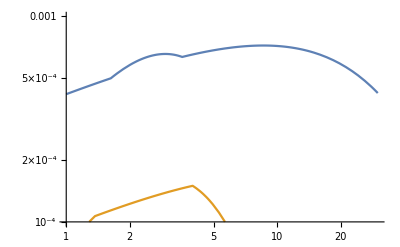

```mathematica
LogLogPlot[{2MaxEnv[x],.5MinEnv[x]},{x,1,30},Exclusions->None,PlotRange->{{1,30},{10^-4,10^-3}}] (* Exclusions because otherwise there are gaps *)
```

#### BottomlessMinEnv

This accounts for the fact that Simona’s green line goes off the chart at 14 GeV, so we should consider it effectively zero for the purposes of envelopes.

```mathematica
MinEnv[x_]:=Piecewise[{{Min[BluLin[x],RedLin[x],GreLin[x]],x<14},{0,x>14}}]
```

#### Map on to GeV

```mathematica
MeVtoGeV=10^-3;
```

```mathematica
MaxEnv[x_]:=MeVtoGeV Max[BluLin[x],RedLin[x],GreLin[x]]
MinEnv[x_]:=MeVtoGeV Piecewise[{{Min[BluLin[x],RedLin[x],GreLin[x]],x<14},{0,x>14}}]
```

## Normalization Code

From Flip: I’m just re-writing the “Normalization test code” section to make it understandable to me. I’ve taken Jordan’s code and re-implemented it in a more modular way. I’ve also made it more flexible by forcing the functions to take more arguments, i.e. nothing hard-coded.

### Generate a range of normalizations with respect to one point

RangeOfNorms outputs a list of normalizations for a function. These normalizations are chosen such that the function is between MinFun/A and A*Max at a point testE. Note that the envelope functions are assumed to already give E^2 dN/dE so had to make sure that the E^2 is included in the comparison. 

Update: changed this to a log scale.

MinMaxNorms assumes the MinEnv and MaxEnv functions above and testing at E=1. This is tested agianst Sieve in Jordan’s functions.

```mathematica
(*RangeOfNorms[fun_,MinFun_,MaxFun_,A_,testE_,numdiv_]:=Range[MinFun[testE]/(A  testE^2 fun[testE]),(A MaxFun[testE])/(testE^2 fun[testE]),(A MaxFun[testE]-MinFun[testE]/A)/(numdiv  testE^2 fun[testE])]*)

RangeOfNorms[fun_,MinFun_,MaxFun_,A_,testE_,numdiv_]:=10^#&/@Range[Log[10,MinFun[testE]/(A  testE^2 fun[testE])],Log[10,(A MaxFun[testE])/(testE^2 fun[testE])],(Log[10,(A MaxFun[testE])/(testE^2 fun[testE])]-Log[10,MinFun[testE]/(A  testE^2 fun[testE])])/numdiv]

MinMaxNorms[fun_,A_,numdiv_]:=RangeOfNorms[fun,MinEnv,MaxEnv,A,1,numdiv]
```

### Check if a function and normalization fit the envelope over a range

Create a function that inputs a function (spectrum) and determines whether it fits in the envelope given by  1/AMinEnv < f < A MaxEnv for a given value of A.

Strategy: sample over several points in the range of interest. The functions are smooth enough that you don’t need to sample many points, but this is computationally inexpensive, anyway.

Sample between minE and maxE, the new function samples on a log scale.

Note: do NOT sample the function beyond the kinematic limit, i.e. if you ask questions about energies above the dark matter mass, then the spectrum = 0 and you don’t pass the “Minimum” envelope, even though this is silly. I should probably only ask about normalizations up to 20 or 30 GeV.

NOTE: Actually, a better way to do this is to use a MinEnv that goes to zero above 14, which is the last data point extracted from Simona’s plot.

Note: Shouldn’t ask about minE below 1 (technically below 1.15) or else you’re asking outside of the interpolation.

```mathematica
InEnvelope[function_,MinFun_,MaxFun_, norm_,A_, numpoints_,minE_,maxE_ (* < 30! *)]:=Module[{samplepoints, bunchobooleans, newnorm,coeff=A},
newnorm=norm;
(*samplepoints=49/numpoints#+1&/@Range[1, 51];*)

(* Identify log sampling in Eγ *)
samplepoints=10^#&/@Range[Log[10,minE],Log[10,maxE],(Log[10,maxE]-Log[10,minE])/numpoints];

bunchobooleans = (newnorm #^2 function[#])-MinFun[#]/A≥0 (*≥ for zero case*) && A MaxFun[#]-(newnorm #^2 function[#])>0 &/@samplepoints;

AllTrue[bunchobooleans,TrueQ]
]

(* shortcut version *)
InMinMaxEnv[fun_,norm_,A_,numpoints_,minE_,maxE_]:=InEnvelope[fun,MinEnv,MaxEnv,norm,A,numpoints,minE,maxE]
```

### Get the good normalizations

Takes a list of normalizations and outputs the list of those which stay within the envelope at all sampling points as described by the parameters of InEnvelope.

```mathematica
GoodNorms[function_,MinEnv_,MaxEnv_,A_,listofnorms_,numpoints_,minE_,maxE_]:=
Select[listofnorms,InEnvelope[function,MinEnv,MaxEnv,#,A,numpoints,minE,maxE]&]

BadNorms[function_,MinEnv_,MaxEnv_,A_,listofnorms_,numpoints_,minE_,maxE_]:=
Select[listofnorms,!InEnvelope[function,MinEnv,MaxEnv,#,A,numpoints,minE,maxE]&]
```

### Plotting the whole thing

```mathematica
SuperPlot[func_,norms_,MinEnv_,MaxEnv_,A_,numchecks_,minE_,maxE_]:=Module[
{goodnorms,badnorms},
goodnorms=GoodNorms[func,MinEnv,MaxEnv,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnv,MaxEnv,A,norms,numchecks,minE,maxE];

LogLogPlot[
Evaluate[Join[
x^2 func[x]#&/@goodnorms,
x^2 func[x]#&/@badnorms,

{MinEnv[x]/A,A MaxEnv[x]}]],
{x,minE,maxE},
PlotStyle->Join[
(* Good Curves: *)
Table[{Darker[Green]},{i,Length[goodnorms]}],
(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small]},{i,Length[badnorms]}],
(* Min/Max curves: *)
{{Black},{Black}}],
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Flux [GeV/cm^2/s]"}
(*PlotTheme->"Detailed"*)
]
]
```

## Tools

### From from parameter point to filename

```mathematica
Filename[path_,parampoint_]:=path<>"_"<>ToString[parampoint[[1]]]<>"_"<>ToString[parampoint[[2]]]<>".dat"

AllFilesExist[listofpaths_]:=AllTrue[FileExistsQ[#]&/@listofpaths,TrueQ]
```

### Primitive Tag

Output model, final state, parameter point, and filename as an early tag.

```mathematica
PreTag[mediator_,finalstate_,parameterpoint_,path_]:=
{mediator,finalstate,parameterpoint,Filename[path,parameterpoint]}
```

### Retrieve Interpolating Function

```mathematica
GetFunc[path_,parampoint_]:=ReadIt[Filename[path,parampoint]][[2]]
```

### Get Good Norms Functions

#### Get Good Norms

Reminder: A is the wiggle room in the Min and Max envelope (2), testpoint is where you sample norms (2 is good), numdiv is the number of lines to check (20), numpoints is the number of energies to check the envelope (20), minE and maxE are the ranges of energies to check (1,30).

```mathematica
GetGoodNorms[func_,MinEnv_,MaxEnv_,A_,testpoint_, numdiv_ (* fine graining *),numpoints_,minE_,maxE_]:=GoodNorms[func,MinEnv,MaxEnv,A,
(*list of norms*)
RangeOfNorms[func,MinEnv,MaxEnv,A,testpoint,numdiv],
numpoints,
minE,
maxE]

(*
GetNormsShort[path_,parampoint_]:=GetGoodNorms[
GetFunc[path,parampoint],
MinEnv,MaxEnv,
2, (* A *)
2, (* test point *)
30, (* num slices *)
30, (* num energies to test *)
1,(* minimum energy to test *) 
100 (* maximum energy to test *)
]

GetRangeShort[path_,parampoint_]:={Min[GetNormsShort[path,parampoint]],Max[GetNormsShort[path,parampoint]]}
*)
```

#### Get Good Norms Short

```mathematica
Awiggle=2; (* the fudge factor in the normalizations *)
testpoint=2; (* 2 GeV is where to sample a range of norms *)
numSlices=30; (* # of lines to test *)
numSamples=20; (* # energies to test *)
minE=1; (* to sample fits *)
maxE=35; (* to sample fits *)

GetGoodNormShort[path_,param_]:=GetGoodNorms[GetFunc[path,param],MinEnv,MaxEnv,Awiggle,testpoint,numSlices,numSamples,minE,maxE]

GetGoodNormRange[path_,param_]:={Max[GetGoodNormShort[path,param]],Min[GetGoodNormShort[path,param]]}
```

### Find minimum A for fit

This is a good measure for how much fudge factor do we need in order to get a given curve to fit inside envelope. In other words, the minimum A measures how big the envelope has to be in order for the curves to fit into the envelope while allowing their overall normalization to float. 

To say it physically: this tells me about compatibility of the shape of the spectrum without regard to the overall normalization.

The idea: Run GetGoodNorms with different values of A and find the minimum value (to some given precision) that gives the requisite wiggle room in the window. 

I’m not sophisticated enough to implement a nice divide-and-conquer search algorithm for this, so I’ll just hard code it in multiple stages by order of magnitude in precision.

#### Saved Version

```mathematica
GetMinA1[func_,MinEnv_,MaxEnv_,testpoint_,numSlices_,numSamples_,minE_,maxE_]:=Module[
{AA=0,Dec=1},
While[
Length[
GetGoodNorms[func,MinEnv,MaxEnv,1+Dec AA, testpoint, numSlices,numSamples,minE,maxE]]==0,
1; (* do nothing *)
AA++
];
If[AA==0,0,AA-1]
(* some special cases pass for norm = 1 + Dec AA = 1 *)
(* in this case we say that norm == 1, not zero *)
(* then because we use (1+A1) as the norm, we need to set AA to 0 *)
]

GetMinA01[func_,MinEnv_,MaxEnv_,testpoint_,numSlices_,numSamples_,minE_,maxE_,A1_ (* output of previous func *)]:=Module[
{AA=0,Dec=.1},
While[
Length[
GetGoodNorms[func,MinEnv,MaxEnv,1 +A1+Dec AA, testpoint, numSlices,numSamples,minE,maxE]]==0,
1; (* do nothing *)
AA++
];
If[AA==0,0,AA-1]
]

GetMinA001[func_,MinEnv_,MaxEnv_,testpoint_,numSlices_,numSamples_,minE_,maxE_,A1_,A01_ (* output of previous func *)]:=Module[
{AA=0,Dec=.01},
While[
Length[
GetGoodNorms[func,MinEnv,MaxEnv,1 +A1+.1 A01+Dec AA, testpoint, numSlices,numSamples,minE,maxE]]==0,
1; (* do nothing *)
AA++
];
AA-1 
]

(* Put these all together *)
```

```mathematica
GetMinA[func_,MinEnv_,MaxEnv_,testpoint_,numSlices_,numSamples_,minE_,maxE_]:=Module[{A1,A01,A001},
A1=GetMinA1[func,MinEnv,MaxEnv,testpoint,numSlices,numSamples,minE,maxE];
A01=GetMinA01[func,MinEnv,MaxEnv,testpoint,numSlices,numSamples,minE,maxE,A1];
A001=GetMinA001[func,MinEnv,MaxEnv,testpoint,numSlices,numSamples,minE,maxE,A1,A01];
1+A1+.1 A01 + .01(A001+1 (* to give the first nonzero value *))
]
```

Actually, an alternate estimated measure of the same quantity is to just check the size of GetGoodNorms---the bigger the spread the less wiggle room you need.

#### New Version: hard stop when you get to large numbers

This now stops at A=10 so there are no more runaways. Thus if the minimum A = 10, then you should treat this as “effectively impossible to find an envelope that works.”

```mathematica
GetMinA1[func_,MinEnv_,MaxEnv_,testpoint_,numSlices_,numSamples_,minE_,maxE_]:=Module[
{AA=0,Dec=1},
While[
Length[
GetGoodNorms[func,MinEnv,MaxEnv,1+Dec AA, testpoint, numSlices,numSamples,minE,maxE]]==0&&AA<10,
(*Print[AA]*)
1; (* do nothing *)
AA++
];
If[AA==0,0,AA-1]
(* some special cases pass for norm = 1 + Dec AA = 1 *)
(* in this case we say that norm == 1, not zero *)
(* then because we use (1+A1) as the norm, we need to set AA to 0 *)
]

GetMinA01[func_,MinEnv_,MaxEnv_,testpoint_,numSlices_,numSamples_,minE_,maxE_,A1_ (* output of previous func *)]:=Module[
{AA=0,Dec=.1},
While[
Length[
GetGoodNorms[func,MinEnv,MaxEnv,1 +A1+Dec AA, testpoint, numSlices,numSamples,minE,maxE]]==0,
1; (* do nothing *)
AA++
];
If[AA==0,0,AA-1]
]

GetMinA001[func_,MinEnv_,MaxEnv_,testpoint_,numSlices_,numSamples_,minE_,maxE_,A1_,A01_ (* output of previous func *)]:=Module[
{AA=0,Dec=.01},
While[
Length[
GetGoodNorms[func,MinEnv,MaxEnv,1 +A1+.1 A01+Dec AA, testpoint, numSlices,numSamples,minE,maxE]]==0,
1; (* do nothing *)
AA++
];
AA-1 
]

(* Put these all together *)
```

```mathematica
GetMinA[func_,MinEnv_,MaxEnv_,testpoint_,numSlices_,numSamples_,minE_,maxE_]:=Module[{A1,A01,A001},
A1=GetMinA1[func,MinEnv,MaxEnv,testpoint,numSlices,numSamples,minE,maxE];
If[A1<7,
A01=GetMinA01[func,MinEnv,MaxEnv,testpoint,numSlices,numSamples,minE,maxE,A1],
A01=0];
If[A1<7,
A001=GetMinA001[func,MinEnv,MaxEnv,testpoint,numSlices,numSamples,minE,maxE,A1,A01],
A001=0];
If[A1<7,
1+A1+.1 A01 + .01(A001+1 (* to give the first nonzero value *)),
10]
]
```

Actually, an alternate estimated measure of the same quantity is to just check the size of GetGoodNorms---the bigger the spread the less wiggle room you need.

### All Information Tag

This should contain all of the information needed for each parameter point.

```mathematica
FullTag[mediator_ (*string*),final_ (*string*),path_,param_,
MinEnv_,MaxEnv_,A_,testpoint_,numSlices_,numSamples_,minE_,maxE_]:=
Module[{func,norms},
func=GetFunc[path,param];
norms=GetGoodNorms[func,MinEnv,MaxEnv,A,testpoint,numSlices,numSamples,minE,maxE];

Join[PreTag[mediator,final,param,path],
{{Min[norms],Max[norms]}},
{GetMinA[func,MinEnv,MaxEnv,testpoint,numSlices,numSamples,minE,maxE]}
]
]
```

Output is:
{
Mediator (“V” or “sc”),
Final state (e.g. “b”),
Parameters (mχ,m_mediator),
Path,
Minimum norm to fit,
Maximum norm to fit,
Minimum A for which the shape fits
}

Note that to convert the min/max norms into cross sections, you need to calculate the J factor for the region of interest from which the min/max curves came.